```mathematica
Clear["Global`*"]
```

```mathematica
inputData = Import[NotebookDirectory[]<>"/input.txt"];
input = StringSplit[inputData];
l=Length[input];(*l will have to be even*)
(*Write a function here that will take in strings as variable names*)
dt=Read[StringToStream[input[[2]]]];
tmax=input[[4]];
nStore=input[[6]];
nTrajectory=input[[8]];
nBin=input[[10]];
yWall=input[[12]];
lambda=input[[14]];
deltaZ=input[[16]];
deltaPz=input[[18]];
transitTime=input[[20]];
density=input[[22]];
rabi=input[[24]];
kappa=input[[26]];
invT2 = input[[28]];
controlType = input[[30]];
name =input[[32]]
```

test

Import::nffil: File not found during Import.

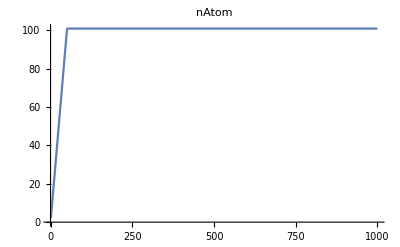

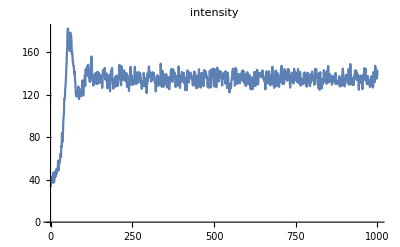

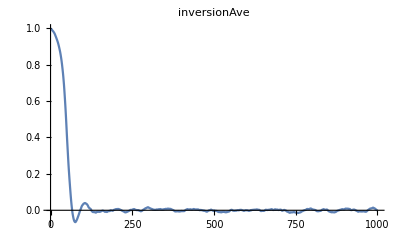

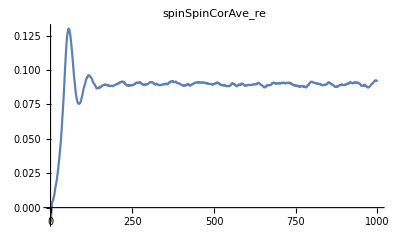

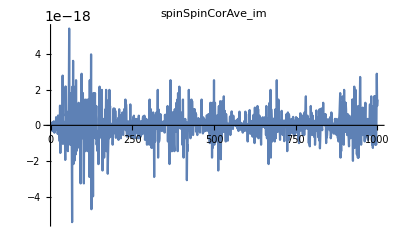

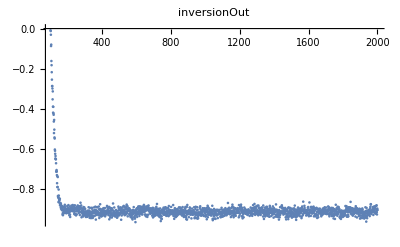

General::sfunc: {{Identity,Identity},{Identity,Identity}} is not a valid scaling function.

General::stop: Further output of General::sfunc will be suppressed during this calculation.

ListLinePlot[$Failed,PlotRange→All,PlotLabel→realG1]

General::sfunc: {{Identity,Identity},{Identity,Identity}} is not a valid scaling function.

General::stop: Further output of General::sfunc will be suppressed during this calculation.

ListLinePlot[$Failed,PlotRange→All,PlotLabel→spectra]

```mathematica
(*When doing one run*)
intensity=Flatten[Import[NotebookDirectory[]<>controlType <>"/"<>name<>"/intensity.dat"]];
nAtom=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/nAtom.dat"]];
inversionAve=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/inversionAve.dat"]];
spinSpinCorAveRe=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/spinSpinCorAve_re.dat"]];
spinSpinCorAveIm=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/spinSpinCorAve_im.dat"]];
spinSpinCorRe=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/spinSpinCor_re.dat"]];
spinSpinCorIm=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/spinSpinCor_im.dat"]];
szMatrix=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/szMatrix.dat"]];
szFinal=Flatten[Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/szFinal.dat"]];
realG1 = Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/realG1.dat"];
spectra=Import[NotebookDirectory[]<>controlType<>"/"<>name<>"/spectra.dat"];
ListLinePlot[nAtom,PlotRange->All,PlotLabel->"nAtom"]
ListLinePlot[intensity,PlotRange->All,PlotLabel->"intensity"]
ListLinePlot[inversionAve,PlotRange->All,PlotLabel->"inversionAve"]
ListLinePlot[spinSpinCorAveRe,PlotRange->All,PlotLabel->"spinSpinCorAve_re"]
ListLinePlot[spinSpinCorAveIm,PlotRange->All,PlotLabel->"spinSpinCorAve_im"]
ListPlot[szFinal,PlotRange->All,PlotLabel->"inversionOut"]
ListLinePlot[realG1,PlotRange->All,PlotLabel->"realG1"]
ListLinePlot[spectra,PlotRange->All,PlotLabel->"spectra"]
```

FittedModel[0.00244474/(0.00196706+4 x^2)]

| Estimate | Standard Error | t-Statistic | P-Value
linewidth | 0.0443516 | 0.0052217 | 8.49371 | 6.42392×10^-17
A | 0.0551219 | 0.001155 | 47.7244 | 3.92966×10^-270

0.0443516

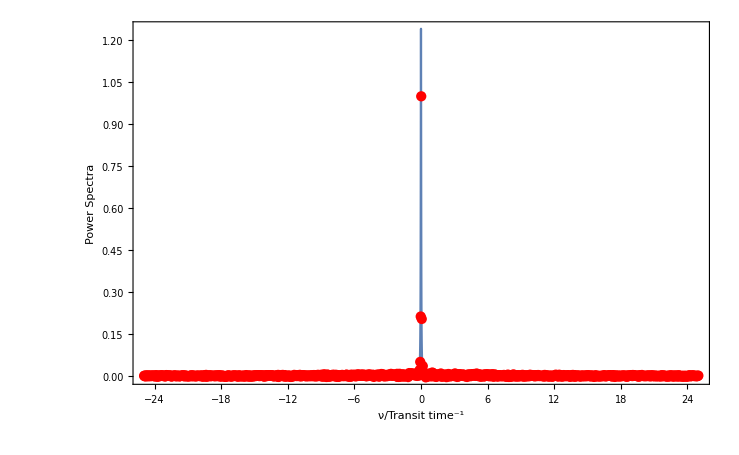

```mathematica
(*Fit the spectra to lorentzian*)
lorentzianModel=A linewidth/(linewidth^2+4x^2);
fitLoren=NonlinearModelFit[spectra,{lorentzianModel},{linewidth,A},{x}]
fitLoren["ParameterTable"]
linewidth1 = linewidth/.fitLoren["BestFitParameters"]
Show[{Plot[fitLoren[x],{x,-5,5},PlotRange->All,BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.01],Map[Point,spectra]}]},Frame->True,FrameLabel->{"ν/Transit time^-1","Power Spectra"}]
```

```mathematica
tauc1=1/(linewidth1 Pi)
```

7.17697

B ⅇ^(-t/tc)

FittedModel[1.09466 ⅇ^(-0.0986906 t)]

| Estimate | Standard Error | t-Statistic | P-Value
tc | 10.1327 | 0.123288 | 82.1868 | 1.04557290129×10^-310
B | 1.09466 | 0.00607949 | 180.058 | 2.11139221705×10^-490

10.1327

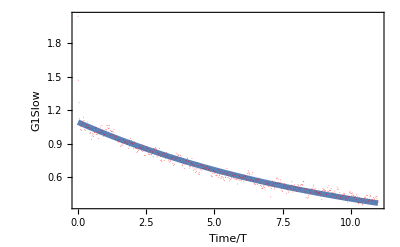

```mathematica
(*Fit the G1 function to exponential*)
exponentialModel=B Exp[- t/tc]
fitExp=NonlinearModelFit[realG1,{exponentialModel},{tc,B},{t}]
fitExp["ParameterTable"]
tauc2=tc/.fitExp["BestFitParameters"]
Show[{Plot[fitExp[x],{x,0,Last[realG1][[1]]},PlotRange->All,PlotStyle->{Thickness[0.01]},BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.001],Map[Point,realG1]}]},Frame->True,FrameLabel->{"Time/T","G1Slow"}]
```

```mathematica
(*Get the linewidth from the coherent time*)
linewidth2 = 1/(tauc2 Pi)
```

0.0314142

```mathematica
(*Notice there is another exponential decay.*)
```

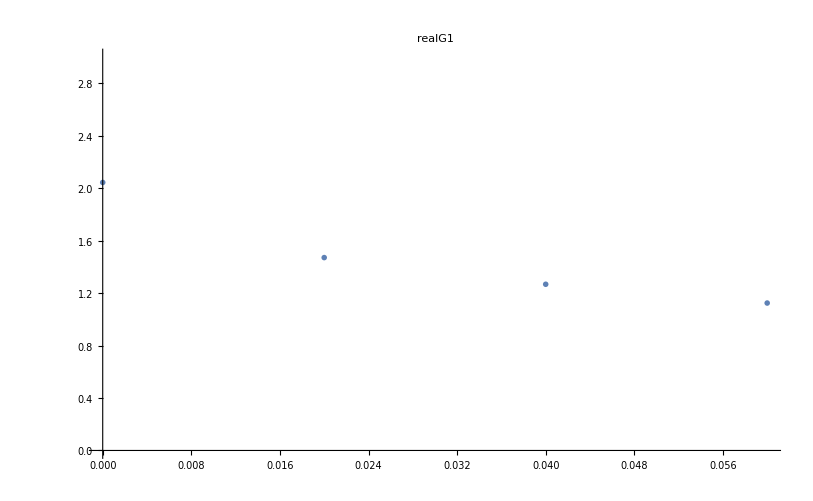

B2 ⅇ^(-linewidthQuick π t)

FittedModel[2.00936 ⅇ^(-12.6741 t)]

| Estimate | Standard Error | t-Statistic | P-Value
linewidthQuick | 4.03429 | 0.817134 | 4.93712 | 0.127224
B2 | 2.00936 | 0.105459 | 19.0535 | 0.0333816

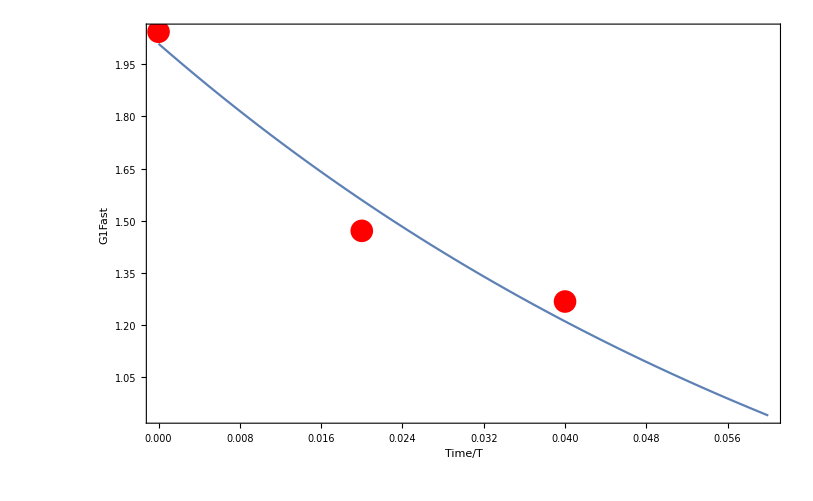

```mathematica
cutOff = 0.06;
ListPlot[realG1,PlotRange->{{0,cutOff},{0,3}}, 
PlotLabel->"realG1",PlotMarkers->{Automatic,Small}]
secondNum=IntegerPart[cutOff/realG1[[2,1]]];
secondExp=Take[realG1,secondNum];
exponentialModel2=B2 Exp[- Pi linewidthQuick t]
fitExp2=NonlinearModelFit[secondExp,{exponentialModel2},{linewidthQuick,B2},{t}]
fitExp2["ParameterTable"]
Show[{Plot[fitExp2[x],{x,0,cutOff},PlotRange->All,BaseStyle->{FontSize->30}],Graphics[{Red,PointSize[.02],Map[Point,secondExp]}]},Frame->True,FrameLabel->{"Time/T","G1Fast"}]
```

```mathematica
secondTc = 1/(linewidthQuick Pi)/.fitExp2["BestFitParameters"]
```

0.078901

```mathematica
Mean[intensity]
```

132.172

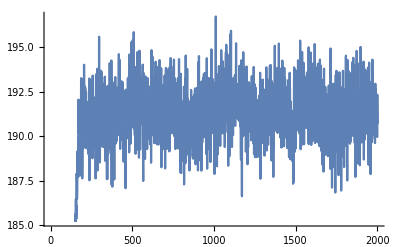

```mathematica
ListLinePlot[ 100*(1-szFinal)]
```

```mathematica
???
```